```mathematica
(*parameters single cell model*)
b1=0.31;
b2=0.20;
gamma=0.27;
alpha=0.94;
vs=0.80;
tita=0.11;
beta=0.88;
aa1=0.5;
bb1=0.5;
cc1=0.5;
(*parameters coupled system*)
k=0.0;
a3=0.26;
de=0.85;
b4=0.35;
a5=0.10;
b5=0.65;
(*goodwin*)
p=15;
(*light*)
L1=0.0;L2=0.0;Tld=24;
(*tiempo*)
tmin=0;tmax=3000;
(*osciladores*)
nodes=10;
(*FUNCIONES*)
L[t_]:=L1+L2*UnitStep[Sin[Pi*t/12]]
Lv2[t_]:=L2 (1+Sin[2 Pi t/Tld])
```

```mathematica
sol1=NDSolve[{
(*oscilador 1*)
x1'[t]==(aa1+bb1*v1[t])/(cc1*v1[t]+(z1[t]^p))-b1*x1[t],    (*mRNA*)
y1'[t]==alpha*x1[t]-(b2+L[t])*y1[t],   (*proteina*)
z1'[t]==beta*y1[t]-gamma*z1[t], (*inhibidor*)
s1'[t]==a3*y1[t]-de*s1[t],   (*neurotransmiter PDF*)
u1'[t]==k*(s2[t]+s3[t]+s4[t]+s5[t]+s6[t]+s7[t]+s8[t]+s9[t]+s10[t])-b4*u1[t], (*Ca2+*)
v1'[t]==a5*u1[t]-b5*v1[t],(*CREB*)
(*oscilador 2*)
x2'[t]==(aa1+bb1*v2[t])/(cc1*v2[t]1+(z2[t]^p))-b1*x2[t],  
y2'[t]==alpha*x2[t]-(b2+L[t])*y2[t],   
z2'[t]==beta*y2[t]-gamma*z2[t],
s2'[t]==a3*y2[t]-de*s2[t],   (*neurotransmiter PDF*)
u2'[t]==k*(s1[t]+s3[t]+s4[t]+s5[t]+s6[t]+s7[t]+s8[t]+s9[t]+s10[t])-b4*u2[t], (*Ca2+*)
v2'[t]==a5*u2[t]-b5*v2[t],(*CREB*)
(*oscilador 3*)
x3'[t]==(aa1+bb1*v3[t])/(cc1*v3[t]+(z3[t]^p))-b1*x3[t],    
y3'[t]==alpha*x3[t]-(b2+L[t])*y3[t],   
z3'[t]==beta*y3[t]-gamma*z3[t],
s3'[t]==a3*y3[t]-de*s3[t],   (*neurotransmiter PDF*)
u3'[t]==k*(s1[t]+s2[t]+s4[t]+s5[t]+s6[t]+s7[t]+s8[t]+s9[t]+s10[t])-b4*u3[t], (*Ca2+*)
v3'[t]==a5*u3[t]-b5*v3[t],(*CREB*)
(*oscilador 4*)
x4'[t]==(aa1+bb1*v4[t])/(cc1*v4[t]+(z4[t]^p))-b1*x4[t],    
y4'[t]==alpha*x4[t]-(b2+L[t])*y4[t],   
z4'[t]==beta*y4[t]-gamma*z4[t],
s4'[t]==a3*y4[t]-de*s4[t],   (*neurotransmiter PDF*)
u4'[t]==k*(s1[t]+s2[t]+s3[t]+s5[t]+s6[t]+s7[t]+s8[t]+s9[t]+s10[t])-b4*u4[t], (*Ca2+*)
v4'[t]==a5*u4[t]-b5*v4[t],(*CREB*)
(*oscilador 5*)
x5'[t]==(aa1+bb1*v5[t])/(cc1*v5[t]+(z5[t]^p))-b1*x5[t],    
y5'[t]==alpha*x5[t]-(b2+L[t])*y5[t],   
z5'[t]==beta*y5[t]-gamma*z5[t],
s5'[t]==a3*y5[t]-de*s5[t],   (*neurotransmiter PDF*)
u5'[t]==k*(s1[t]+s2[t]+s3[t]+s4[t]+s6[t]+s7[t]+s8[t]+s9[t]+s10[t])-b4*u5[t], (*Ca2+*)
v5'[t]==a5*u5[t]-b5*v5[t],(*CREB*)
(*oscilador 6*)
x6'[t]==(aa1+bb1*v6[t])/(cc1*v6[t]+(z6[t]^p))-b1*x6[t],    
y6'[t]==alpha*x6[t]-(b2+L[t])*y6[t],   
z6'[t]==beta*y6[t]-gamma*z6[t],
s6'[t]==a3*y6[t]-de*s6[t],   (*neurotransmiter PDF*)
u6'[t]==k*(s1[t]+s2[t]+s3[t]+s4[t]+s5[t]+s7[t]+s8[t]+s9[t]+s10[t])-b4*u6[t], (*Ca2+*)
v6'[t]==a5*u6[t]-b5*v6[t],(*CREB*)
(*oscilador 7*)
x7'[t]==(aa1+bb1*v7[t])/(cc1*v7[t]+(z7[t]^p))-b1*x7[t],    
y7'[t]==alpha*x7[t]-(b2+L[t])*y7[t],   
z7'[t]==beta*y7[t]-gamma*z7[t],
s7'[t]==a3*y7[t]-de*s7[t],   (*neurotransmiter PDF*)
u7'[t]==k*(s1[t]+s2[t]+s3[t]+s4[t]+s5[t]+s6[t]+s8[t]+s9[t]+s10[t])-b4*u7[t], (*Ca2+*)
v7'[t]==a5*u7[t]-b5*v7[t],(*CREB*)
(*oscilador 8*)
x8'[t]==(aa1+bb1*v8[t])/(cc1*v8[t]+(z8[t]^p))-b1*x8[t],    
y8'[t]==alpha*x8[t]-(b2+L[t])*y8[t],   
z8'[t]==beta*y8[t]-gamma*z8[t],
s8'[t]==a3*y8[t]-de*s8[t],   (*neurotransmiter PDF*)
u8'[t]==k*(s1[t]+s2[t]+s3[t]+s4[t]+s5[t]+s6[t]+s7[t]+s9[t]+s10[t])-b4*u8[t], (*Ca2+*)
v8'[t]==a5*u8[t]-b5*v8[t],(*CREB*)
(*oscilador 9*)
x9'[t]==(aa1+bb1*v9[t])/(cc1*v9[t]+(z9[t]^p))-b1*x9[t],    
y9'[t]==alpha*x9[t]-(b2+L[t])*y9[t],   
z9'[t]==beta*y9[t]-gamma*z9[t],
s9'[t]==a3*y9[t]-de*s9[t],   (*neurotransmiter PDF*)
u9'[t]==k*(s1[t]+s2[t]+s3[t]+s4[t]+s5[t]+s6[t]+s7[t]+s8[t]+s10[t])-b4*u4[t], (*Ca2+*)
v9'[t]==a5*u9[t]-b5*v9[t],(*CREB*)
(*oscilador 10*)
x10'[t]==(aa1+bb1*v10[t])/(cc1*v10[t]+(z10[t]^p))-b1*x10[t],    
y10'[t]==alpha*x10[t]-(b2+L[t])*y10[t],   
z10'[t]==beta*y10[t]-gamma*z10[t],
s10'[t]==a3*y10[t]-de*s10[t],   (*neurotransmiter PDF*)
u10'[t]==k*(s1[t]+s2[t]+s3[t]+s4[t]+s5[t]+s6[t]+s7[t]+s8[t]+s9[t])-b4*u10[t], (*Ca2+*)
v10'[t]==a5*u10[t]-b5*v10[t],(*CREB*)
(*condiciones iniciales*)
x1[tmin]==0.17,y1[tmin]==0.1,z1[tmin]==0.5,s1[tmin]==0.32,u1[tmin]==0.4,v1[tmin]==0.1,
x2[tmin]==0.17,y2[tmin]==0.2,z2[tmin]==0.5,s2[tmin]==0.32,u2[tmin]==0.4,v2[tmin]==0.1,
x3[tmin]==0.17,y3[tmin]==0.3,z3[tmin]==0.5,s3[tmin]==0.32,u3[tmin]==0.4,v3[tmin]==0.1,
x4[tmin]==0.17,y4[tmin]==0.4,z4[tmin]==0.5,s4[tmin]==0.32,u4[tmin]==0.4,v4[tmin]==0.1,
x5[tmin]==0.17,y5[tmin]==0.5,z5[tmin]==0.5,s5[tmin]==0.32,u5[tmin]==0.4,v5[tmin]==0.1,
x6[tmin]==0.17,y6[tmin]==0.6,z6[tmin]==0.5,s6[tmin]==0.32,u6[tmin]==0.4,v6[tmin]==0.1,
x7[tmin]==0.17,y7[tmin]==0.7,z7[tmin]==0.5,s7[tmin]==0.32,u7[tmin]==0.4,v7[tmin]==0.1,
x8[tmin]==0.17,y8[tmin]==0.8,z8[tmin]==0.5,s8[tmin]==0.32,u8[tmin]==0.4,v8[tmin]==0.1,
x9[tmin]==0.17,y9[tmin]==0.9,z9[tmin]==0.5,s9[tmin]==0.32,u9[tmin]==0.4,v9[tmin]==0.1,
x10[tmin]==0.17,y10[tmin]==1.0,z10[tmin]==0.5,s10[tmin]==0.32,u10[tmin]==0.4,v10[tmin]==0.1},
 {x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,s1,s2,s3,s4,s5,s6,s7,s8,s9,s10,u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10},{t,tmin,tmax},MaxSteps->10^6,PrecisionGoal->5,AccuracyGoal->5];
```

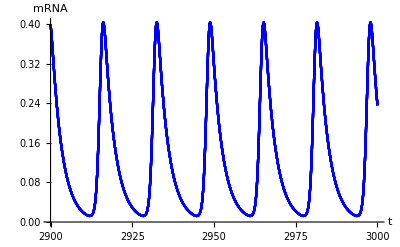

```mathematica
Plot[Evaluate[{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t]}/.sol1],{t,2900,3000},PlotStyle->{ Blue},AxesLabel->{"t","mRNA"}]
```

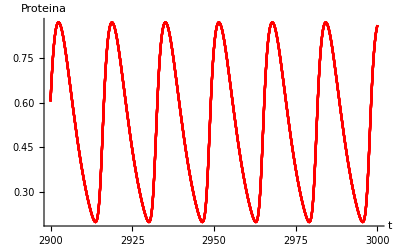

```mathematica
Plot[Evaluate[{y1[t],y2[t],y3[t],y4[t],y5[t],y6[t],y7[t],y8[t],y9[t],y10[t]}/.sol1],{t,2900,3000},PlotStyle->{ Red},AxesLabel->{"t","Proteina"}]
```

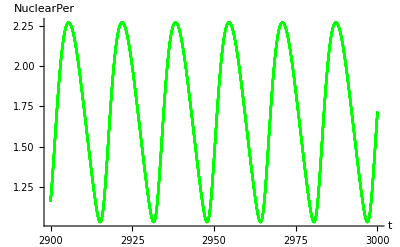

```mathematica
Plot[Evaluate[{z1[t],z2[t],z3[t],z4[t],z5[t],z6[t],z7[t],z8[t],z9[t],z10[t]}/.sol1],{t,2900,3000},PlotStyle->{ Green},AxesLabel->{"t","NuclearPer"}]
```

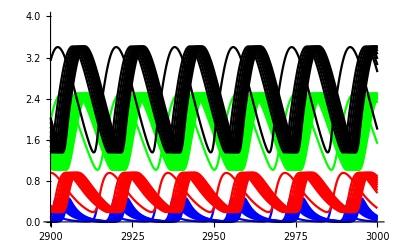

```mathematica
Show[Plot[Evaluate[{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t]}/.sol1],{t,2900,3000},PlotStyle->{Blue},PlotRange->{{2900,3000},{0,4}}],Plot[Evaluate[{y1[t],y2[t],y3[t],y4[t],y5[t],y6[t],y7[t],y8[t],y9[t],y10[t]}/.sol1],{t,2900,3000},PlotStyle->{Red},PlotRange->{{2900,3000},{0,4}}],Plot[Evaluate[{z1[t],z2[t],z3[t],z4[t],z5[t],z6[t],z7[t],z8[t],z9[t],z10[t]}/.sol1],{t,2900,3000},PlotStyle->{Green},PlotRange->{{2900,3000},{0,4}}],Plot[Evaluate[{x1[t]+y1[t]+z1[t],x2[t]+y2[t]+z2[t],x3[t]+y3[t]+z3[t],x4[t]+y4[t]+z4[t],x5[t]+y5[t]+z5[t],x6[t]+y6[t]+z6[t],x7[t]+y7[t]+z7[t],x8[t]+y8[t]+z8[t],x9[t]+y9[t]+z9[t],x10[t]+y10[t]+z10[t]}/.sol1],{t,2900,3000},PlotStyle->{Black},PlotRange->{{2900,3000},{0,4}}]]
```